```mathematica
Directory[]
```

/home/milan

```mathematica
ψ[μ_,L_]:=∑_(n=0)^L (2n+1)/2 LegendreP[n,μ] Subscript[ϕ, n][z]
```

```mathematica
L=9;
```

Replace Q by ⅆ/ⅆz

```mathematica
P[n_]=(n+1)/(2n+1)Q Subscript[ϕ, n+1][z] +n/(2n+1)Q Subscript[ϕ, n-1][z]+Subscript[Σ, a,n][z]Subscript[ϕ, n][z]==Subscript[S, n][z]
```

(n Q ϕ_(-1+n)[z])/(1+2 n)+((1+n) Q ϕ_(1+n)[z])/(1+2 n)+ϕ_n[z] Σ_(a,n)[z]==S_n[z]

```mathematica
eqns=Table[P[n]/.If[n≥1, Subscript[S, n][z]->0,Subscript[S, n][z]->Subscript[S, n][z]],{n,0,L}]/.Subscript[ϕ, L+1][z]->0;
```

```mathematica
MatrixForm[eqns]
```

(Q ϕ_1[z]+ϕ_0[z] Σ_(a,0)[z]==S_0[z]
1/3 Q ϕ_0[z]+2/3 Q ϕ_2[z]+ϕ_1[z] Σ_(a,1)[z]==0
2/5 Q ϕ_1[z]+3/5 Q ϕ_3[z]+ϕ_2[z] Σ_(a,2)[z]==0
3/7 Q ϕ_2[z]+4/7 Q ϕ_4[z]+ϕ_3[z] Σ_(a,3)[z]==0
4/9 Q ϕ_3[z]+5/9 Q ϕ_5[z]+ϕ_4[z] Σ_(a,4)[z]==0
5/11 Q ϕ_4[z]+6/11 Q ϕ_6[z]+ϕ_5[z] Σ_(a,5)[z]==0
6/13 Q ϕ_5[z]+7/13 Q ϕ_7[z]+ϕ_6[z] Σ_(a,6)[z]==0
7/15 Q ϕ_6[z]+8/15 Q ϕ_8[z]+ϕ_7[z] Σ_(a,7)[z]==0
8/17 Q ϕ_7[z]+9/17 Q ϕ_9[z]+ϕ_8[z] Σ_(a,8)[z]==0
9/19 Q ϕ_8[z]+ϕ_9[z] Σ_(a,9)[z]==0)

```mathematica
oddn=Table[2n-1,{n,1,(L+1)/2}];
evenn=Table[2n,{n,1,(L+1)/2}];
```

```mathematica
oddmom=Table[Subscript[ϕ, n][z],{n,0,L}][[evenn]]
evenmom=Table[Subscript[ϕ, n][z],{n,0,L}][[oddn]]
```

{ϕ_1[z],ϕ_3[z],ϕ_5[z],ϕ_7[z],ϕ_9[z]}

{ϕ_0[z],ϕ_2[z],ϕ_4[z],ϕ_6[z],ϕ_8[z]}

```mathematica
oddWrtEven=Solve[eqns[[evenn]],oddmom]
```

{{ϕ_1[z]→(-Q ϕ_0[z]-2 Q ϕ_2[z])/(3 Σ_(a,1)[z]),ϕ_3[z]→(-3 Q ϕ_2[z]-4 Q ϕ_4[z])/(7 Σ_(a,3)[z]),ϕ_5[z]→(-5 Q ϕ_4[z]-6 Q ϕ_6[z])/(11 Σ_(a,5)[z]),ϕ_7[z]→(-7 Q ϕ_6[z]-8 Q ϕ_8[z])/(15 Σ_(a,7)[z]),ϕ_9[z]→-(9 Q ϕ_8[z])/(19 Σ_(a,9)[z])}}

```mathematica
SPL=eqns[[oddn]]/.oddWrtEven[[1]]/.Subscript[S, 0][z]->Subscript[νΣ, f] Subscript[ϕ, 0][z];
```

```mathematica
MatrixForm[SPL]
```

(ϕ_0[z] Σ_(a,0)[z]+(Q (-Q ϕ_0[z]-2 Q ϕ_2[z]))/(3 Σ_(a,1)[z])==νΣ_f ϕ_0[z]
(2 Q (-Q ϕ_0[z]-2 Q ϕ_2[z]))/(15 Σ_(a,1)[z])+ϕ_2[z] Σ_(a,2)[z]+(3 Q (-3 Q ϕ_2[z]-4 Q ϕ_4[z]))/(35 Σ_(a,3)[z])==0
(4 Q (-3 Q ϕ_2[z]-4 Q ϕ_4[z]))/(63 Σ_(a,3)[z])+ϕ_4[z] Σ_(a,4)[z]+(5 Q (-5 Q ϕ_4[z]-6 Q ϕ_6[z]))/(99 Σ_(a,5)[z])==0
(6 Q (-5 Q ϕ_4[z]-6 Q ϕ_6[z]))/(143 Σ_(a,5)[z])+ϕ_6[z] Σ_(a,6)[z]+(7 Q (-7 Q ϕ_6[z]-8 Q ϕ_8[z]))/(195 Σ_(a,7)[z])==0
(8 Q (-7 Q ϕ_6[z]-8 Q ϕ_8[z]))/(255 Σ_(a,7)[z])+ϕ_8[z] Σ_(a,8)[z]-(81 Q^2 ϕ_8[z])/(323 Σ_(a,9)[z])==0)

```mathematica
oddPseudoFluxes=Table[(n+1) Subscript[ϕ, n+1][z] +n Subscript[ϕ, n-1][z]==Subscript[F, n][z],{n,1,L,2}]/.Subscript[ϕ, L+1][z]->0
pseudoDiffusions=Table[1/((2n+1)Subscript[Σ, a,n][z])->Subscript[D, n][z],{n,1,L,2}]
```

{ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]}

{1/(3 Σ_(a,1)[z])→D_1[z],1/(7 Σ_(a,3)[z])→D_3[z],1/(11 Σ_(a,5)[z])→D_5[z],1/(15 Σ_(a,7)[z])→D_7[z],1/(19 Σ_(a,9)[z])→D_9[z]}

```mathematica
Table[Subscript[ϕ, 2i][z]/.Solve[Eliminate[oddPseudoFluxes,Drop[evenmom,{i+1}]],Subscript[ϕ, 2i][z]]//First//Expand,{i,0,(L-1)/2}]//MatrixForm
```

(F_1[z]-(2 F_3[z])/3+(8 F_5[z])/15-(16 F_7[z])/35+(128 F_9[z])/315
F_3[z]/3-(4 F_5[z])/15+(8 F_7[z])/35-(64 F_9[z])/315
F_5[z]/5-(6 F_7[z])/35+(16 F_9[z])/105
F_7[z]/7-(8 F_9[z])/63
F_9[z]/9)

```mathematica
lower=Table[n/(2n+1),{n,2,L,2}]
centr=Table[(n+1)/(2n+1),{n,0,L,2}]
```

{2/5,4/9,6/13,8/17}

{1,3/5,5/9,7/13,9/17}

```mathematica
Adata=If[L>1,{Band[{2,1}]->lower,Band[{1,1}]->centr},{Band[{1,1}]->centr}];
```

```mathematica
A=SparseArray[Adata,Floor[L/2]+1];
```

```mathematica
A//Normal//MatrixForm
```

(1 | 0 | 0 | 0 | 0
2/5 | 3/5 | 0 | 0 | 0
0 | 4/9 | 5/9 | 0 | 0
0 | 0 | 6/13 | 7/13 | 0
0 | 0 | 0 | 8/17 | 9/17)

```mathematica
Map[MatrixForm[#]&,JordanDecomposition[A]]
```

{(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1/500 | 1
0 | 0 | 1/486 | 1/50 | 1
0 | 1/52 | 1/18 | 3/20 | 1
1 | 1 | 1 | 1 | 1),(9/17 | 0 | 0 | 0 | 0
0 | 7/13 | 0 | 0 | 0
0 | 0 | 5/9 | 0 | 0
0 | 0 | 0 | 3/5 | 0
0 | 0 | 0 | 0 | 1)}

```mathematica
rhs=Table[Subscript[Σ, a,n][z]Subscript[ϕ, n][z],{n,0,L,2}];
rhs[[1]]=rhs[[1]]-Subscript[νΣ, f] Subscript[ϕ, 0][z];
```

```mathematica
DelDDelFs=Table[Subscript[DelDDelF, n],{n,1,L,2}];
```

```mathematica
eqnsForDelDDelFs1=Thread[DelDDelFs==LinearSolve[A,rhs]]
```

{DelDDelF_1==-νΣ_f ϕ_0[z]+ϕ_0[z] Σ_(a,0)[z],DelDDelF_3==2/3 νΣ_f ϕ_0[z]-2/3 ϕ_0[z] Σ_(a,0)[z]+5/3 ϕ_2[z] Σ_(a,2)[z],DelDDelF_5==-8/15 νΣ_f ϕ_0[z]+8/15 ϕ_0[z] Σ_(a,0)[z]-4/3 ϕ_2[z] Σ_(a,2)[z]+9/5 ϕ_4[z] Σ_(a,4)[z],DelDDelF_7==16/35 νΣ_f ϕ_0[z]-16/35 ϕ_0[z] Σ_(a,0)[z]+8/7 ϕ_2[z] Σ_(a,2)[z]-54/35 ϕ_4[z] Σ_(a,4)[z]+13/7 ϕ_6[z] Σ_(a,6)[z],DelDDelF_9==1/315 (-128 νΣ_f ϕ_0[z]+128 ϕ_0[z] Σ_(a,0)[z]-320 ϕ_2[z] Σ_(a,2)[z]+432 ϕ_4[z] Σ_(a,4)[z]-520 ϕ_6[z] Σ_(a,6)[z]+595 ϕ_8[z] Σ_(a,8)[z])}

```mathematica
eqnsForDelDDelFs2=Map[Join[{#},oddPseudoFluxes]&,eqnsForDelDDelFs1]
```

{{DelDDelF_1==-νΣ_f ϕ_0[z]+ϕ_0[z] Σ_(a,0)[z],ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DelDDelF_3==2/3 νΣ_f ϕ_0[z]-2/3 ϕ_0[z] Σ_(a,0)[z]+5/3 ϕ_2[z] Σ_(a,2)[z],ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DelDDelF_5==-8/15 νΣ_f ϕ_0[z]+8/15 ϕ_0[z] Σ_(a,0)[z]-4/3 ϕ_2[z] Σ_(a,2)[z]+9/5 ϕ_4[z] Σ_(a,4)[z],ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DelDDelF_7==16/35 νΣ_f ϕ_0[z]-16/35 ϕ_0[z] Σ_(a,0)[z]+8/7 ϕ_2[z] Σ_(a,2)[z]-54/35 ϕ_4[z] Σ_(a,4)[z]+13/7 ϕ_6[z] Σ_(a,6)[z],ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DelDDelF_9==1/315 (-128 νΣ_f ϕ_0[z]+128 ϕ_0[z] Σ_(a,0)[z]-320 ϕ_2[z] Σ_(a,2)[z]+432 ϕ_4[z] Σ_(a,4)[z]-520 ϕ_6[z] Σ_(a,6)[z]+595 ϕ_8[z] Σ_(a,8)[z]),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]}}

```mathematica
eqnsForDelDDelFs3=Map[Eliminate[#,evenmom]&,eqnsForDelDDelFs2]
```

{-315 DelDDelF_1+210 νΣ_f F_3[z]-168 νΣ_f F_5[z]+144 νΣ_f F_7[z]-128 νΣ_f F_9[z]-210 F_3[z] Σ_(a,0)[z]+168 F_5[z] Σ_(a,0)[z]-144 F_7[z] Σ_(a,0)[z]+128 F_9[z] Σ_(a,0)[z]==F_1[z] (315 νΣ_f-315 Σ_(a,0)[z]),945 DelDDelF_3+420 νΣ_f F_3[z]-336 νΣ_f F_5[z]+288 νΣ_f F_7[z]-256 νΣ_f F_9[z]-420 F_3[z] Σ_(a,0)[z]+336 F_5[z] Σ_(a,0)[z]-288 F_7[z] Σ_(a,0)[z]+256 F_9[z] Σ_(a,0)[z]-525 F_3[z] Σ_(a,2)[z]+420 F_5[z] Σ_(a,2)[z]-360 F_7[z] Σ_(a,2)[z]+320 F_9[z] Σ_(a,2)[z]==F_1[z] (630 νΣ_f-630 Σ_(a,0)[z]),-4725 DelDDelF_5+1680 νΣ_f F_3[z]-1344 νΣ_f F_5[z]+1152 νΣ_f F_7[z]-1024 νΣ_f F_9[z]-1680 F_3[z] Σ_(a,0)[z]+1344 F_5[z] Σ_(a,0)[z]-1152 F_7[z] Σ_(a,0)[z]+1024 F_9[z] Σ_(a,0)[z]-2100 F_3[z] Σ_(a,2)[z]+1680 F_5[z] Σ_(a,2)[z]-1440 F_7[z] Σ_(a,2)[z]+1280 F_9[z] Σ_(a,2)[z]+1701 F_5[z] Σ_(a,4)[z]-1458 F_7[z] Σ_(a,4)[z]+1296 F_9[z] Σ_(a,4)[z]==F_1[z] (2520 νΣ_f-2520 Σ_(a,0)[z]),11025 DelDDelF_7+3360 νΣ_f F_3[z]-2688 νΣ_f F_5[z]+2304 νΣ_f F_7[z]-2048 νΣ_f F_9[z]-3360 F_3[z] Σ_(a,0)[z]+2688 F_5[z] Σ_(a,0)[z]-2304 F_7[z] Σ_(a,0)[z]+2048 F_9[z] Σ_(a,0)[z]-4200 F_3[z] Σ_(a,2)[z]+3360 F_5[z] Σ_(a,2)[z]-2880 F_7[z] Σ_(a,2)[z]+2560 F_9[z] Σ_(a,2)[z]+3402 F_5[z] Σ_(a,4)[z]-2916 F_7[z] Σ_(a,4)[z]+2592 F_9[z] Σ_(a,4)[z]-2925 F_7[z] Σ_(a,6)[z]+2600 F_9[z] Σ_(a,6)[z]==F_1[z] (5040 νΣ_f-5040 Σ_(a,0)[z]),-99225 DelDDelF_9+26880 νΣ_f F_3[z]-21504 νΣ_f F_5[z]+18432 νΣ_f F_7[z]-16384 νΣ_f F_9[z]-26880 F_3[z] Σ_(a,0)[z]+21504 F_5[z] Σ_(a,0)[z]-18432 F_7[z] Σ_(a,0)[z]+16384 F_9[z] Σ_(a,0)[z]-33600 F_3[z] Σ_(a,2)[z]+26880 F_5[z] Σ_(a,2)[z]-23040 F_7[z] Σ_(a,2)[z]+20480 F_9[z] Σ_(a,2)[z]+27216 F_5[z] Σ_(a,4)[z]-23328 F_7[z] Σ_(a,4)[z]+20736 F_9[z] Σ_(a,4)[z]-23400 F_7[z] Σ_(a,6)[z]+20800 F_9[z] Σ_(a,6)[z]+20825 F_9[z] Σ_(a,8)[z]==F_1[z] (40320 νΣ_f-40320 Σ_(a,0)[z])}

```mathematica
coefAtDs=Thread[Coefficient[eqnsForDelDDelFs3/.Equal->Plus,DelDDelFs]]
```

{-315,945,-4725,11025,-99225}

```mathematica
eqnsForDelDDelFs4=Thread[Thread[Expand[eqnsForDelDDelFs3[[All,1]]/coefAtDs]]==Thread[Expand[eqnsForDelDDelFs3[[All,2]]/coefAtDs]]]
```

{DelDDelF_1-2/3 νΣ_f F_3[z]+8/15 νΣ_f F_5[z]-16/35 νΣ_f F_7[z]+128/315 νΣ_f F_9[z]+2/3 F_3[z] Σ_(a,0)[z]-8/15 F_5[z] Σ_(a,0)[z]+16/35 F_7[z] Σ_(a,0)[z]-128/315 F_9[z] Σ_(a,0)[z]==-νΣ_f F_1[z]+F_1[z] Σ_(a,0)[z],DelDDelF_3+4/9 νΣ_f F_3[z]-16/45 νΣ_f F_5[z]+32/105 νΣ_f F_7[z]-256/945 νΣ_f F_9[z]-4/9 F_3[z] Σ_(a,0)[z]+16/45 F_5[z] Σ_(a,0)[z]-32/105 F_7[z] Σ_(a,0)[z]+256/945 F_9[z] Σ_(a,0)[z]-5/9 F_3[z] Σ_(a,2)[z]+4/9 F_5[z] Σ_(a,2)[z]-8/21 F_7[z] Σ_(a,2)[z]+64/189 F_9[z] Σ_(a,2)[z]==2/3 νΣ_f F_1[z]-2/3 F_1[z] Σ_(a,0)[z],DelDDelF_5-16/45 νΣ_f F_3[z]+64/225 νΣ_f F_5[z]-128/525 νΣ_f F_7[z]+(1024 νΣ_f F_9[z])/4725+16/45 F_3[z] Σ_(a,0)[z]-64/225 F_5[z] Σ_(a,0)[z]+128/525 F_7[z] Σ_(a,0)[z]-(1024 F_9[z] Σ_(a,0)[z])/4725+4/9 F_3[z] Σ_(a,2)[z]-16/45 F_5[z] Σ_(a,2)[z]+32/105 F_7[z] Σ_(a,2)[z]-256/945 F_9[z] Σ_(a,2)[z]-9/25 F_5[z] Σ_(a,4)[z]+54/175 F_7[z] Σ_(a,4)[z]-48/175 F_9[z] Σ_(a,4)[z]==-8/15 νΣ_f F_1[z]+8/15 F_1[z] Σ_(a,0)[z],DelDDelF_7+32/105 νΣ_f F_3[z]-128/525 νΣ_f F_5[z]+(256 νΣ_f F_7[z])/1225-(2048 νΣ_f F_9[z])/11025-32/105 F_3[z] Σ_(a,0)[z]+128/525 F_5[z] Σ_(a,0)[z]-(256 F_7[z] Σ_(a,0)[z])/1225+(2048 F_9[z] Σ_(a,0)[z])/11025-8/21 F_3[z] Σ_(a,2)[z]+32/105 F_5[z] Σ_(a,2)[z]-64/245 F_7[z] Σ_(a,2)[z]+(512 F_9[z] Σ_(a,2)[z])/2205+54/175 F_5[z] Σ_(a,4)[z]-(324 F_7[z] Σ_(a,4)[z])/1225+(288 F_9[z] Σ_(a,4)[z])/1225-13/49 F_7[z] Σ_(a,6)[z]+104/441 F_9[z] Σ_(a,6)[z]==16/35 νΣ_f F_1[z]-16/35 F_1[z] Σ_(a,0)[z],DelDDelF_9-256/945 νΣ_f F_3[z]+(1024 νΣ_f F_5[z])/4725-(2048 νΣ_f F_7[z])/11025+(16384 νΣ_f F_9[z])/99225+256/945 F_3[z] Σ_(a,0)[z]-(1024 F_5[z] Σ_(a,0)[z])/4725+(2048 F_7[z] Σ_(a,0)[z])/11025-(16384 F_9[z] Σ_(a,0)[z])/99225+64/189 F_3[z] Σ_(a,2)[z]-256/945 F_5[z] Σ_(a,2)[z]+(512 F_7[z] Σ_(a,2)[z])/2205-(4096 F_9[z] Σ_(a,2)[z])/19845-48/175 F_5[z] Σ_(a,4)[z]+(288 F_7[z] Σ_(a,4)[z])/1225-(256 F_9[z] Σ_(a,4)[z])/1225+104/441 F_7[z] Σ_(a,6)[z]-(832 F_9[z] Σ_(a,6)[z])/3969-17/81 F_9[z] Σ_(a,8)[z]==-128/315 νΣ_f F_1[z]+128/315 F_1[z] Σ_(a,0)[z]}

```mathematica
eqnsForDelDDelFs5=eqnsForDelDDelFs4/.Thread[DelDDelFs->Table[Subscript[DelDDel, n][z]Subscript[F, n][z],{n,1,L,2}]]
```

{DelDDel_1[z] F_1[z]-2/3 νΣ_f F_3[z]+8/15 νΣ_f F_5[z]-16/35 νΣ_f F_7[z]+128/315 νΣ_f F_9[z]+2/3 F_3[z] Σ_(a,0)[z]-8/15 F_5[z] Σ_(a,0)[z]+16/35 F_7[z] Σ_(a,0)[z]-128/315 F_9[z] Σ_(a,0)[z]==-νΣ_f F_1[z]+F_1[z] Σ_(a,0)[z],4/9 νΣ_f F_3[z]+DelDDel_3[z] F_3[z]-16/45 νΣ_f F_5[z]+32/105 νΣ_f F_7[z]-256/945 νΣ_f F_9[z]-4/9 F_3[z] Σ_(a,0)[z]+16/45 F_5[z] Σ_(a,0)[z]-32/105 F_7[z] Σ_(a,0)[z]+256/945 F_9[z] Σ_(a,0)[z]-5/9 F_3[z] Σ_(a,2)[z]+4/9 F_5[z] Σ_(a,2)[z]-8/21 F_7[z] Σ_(a,2)[z]+64/189 F_9[z] Σ_(a,2)[z]==2/3 νΣ_f F_1[z]-2/3 F_1[z] Σ_(a,0)[z],-16/45 νΣ_f F_3[z]+64/225 νΣ_f F_5[z]+DelDDel_5[z] F_5[z]-128/525 νΣ_f F_7[z]+(1024 νΣ_f F_9[z])/4725+16/45 F_3[z] Σ_(a,0)[z]-64/225 F_5[z] Σ_(a,0)[z]+128/525 F_7[z] Σ_(a,0)[z]-(1024 F_9[z] Σ_(a,0)[z])/4725+4/9 F_3[z] Σ_(a,2)[z]-16/45 F_5[z] Σ_(a,2)[z]+32/105 F_7[z] Σ_(a,2)[z]-256/945 F_9[z] Σ_(a,2)[z]-9/25 F_5[z] Σ_(a,4)[z]+54/175 F_7[z] Σ_(a,4)[z]-48/175 F_9[z] Σ_(a,4)[z]==-8/15 νΣ_f F_1[z]+8/15 F_1[z] Σ_(a,0)[z],32/105 νΣ_f F_3[z]-128/525 νΣ_f F_5[z]+(256 νΣ_f F_7[z])/1225+DelDDel_7[z] F_7[z]-(2048 νΣ_f F_9[z])/11025-32/105 F_3[z] Σ_(a,0)[z]+128/525 F_5[z] Σ_(a,0)[z]-(256 F_7[z] Σ_(a,0)[z])/1225+(2048 F_9[z] Σ_(a,0)[z])/11025-8/21 F_3[z] Σ_(a,2)[z]+32/105 F_5[z] Σ_(a,2)[z]-64/245 F_7[z] Σ_(a,2)[z]+(512 F_9[z] Σ_(a,2)[z])/2205+54/175 F_5[z] Σ_(a,4)[z]-(324 F_7[z] Σ_(a,4)[z])/1225+(288 F_9[z] Σ_(a,4)[z])/1225-13/49 F_7[z] Σ_(a,6)[z]+104/441 F_9[z] Σ_(a,6)[z]==16/35 νΣ_f F_1[z]-16/35 F_1[z] Σ_(a,0)[z],-256/945 νΣ_f F_3[z]+(1024 νΣ_f F_5[z])/4725-(2048 νΣ_f F_7[z])/11025+(16384 νΣ_f F_9[z])/99225+DelDDel_9[z] F_9[z]+256/945 F_3[z] Σ_(a,0)[z]-(1024 F_5[z] Σ_(a,0)[z])/4725+(2048 F_7[z] Σ_(a,0)[z])/11025-(16384 F_9[z] Σ_(a,0)[z])/99225+64/189 F_3[z] Σ_(a,2)[z]-256/945 F_5[z] Σ_(a,2)[z]+(512 F_7[z] Σ_(a,2)[z])/2205-(4096 F_9[z] Σ_(a,2)[z])/19845-48/175 F_5[z] Σ_(a,4)[z]+(288 F_7[z] Σ_(a,4)[z])/1225-(256 F_9[z] Σ_(a,4)[z])/1225+104/441 F_7[z] Σ_(a,6)[z]-(832 F_9[z] Σ_(a,6)[z])/3969-17/81 F_9[z] Σ_(a,8)[z]==-128/315 νΣ_f F_1[z]+128/315 F_1[z] Σ_(a,0)[z]}

```mathematica
{b,m}=CoefficientArrays[eqnsForDelDDelFs5,Table[Subscript[F, n][z],{n,1,L,2}]]
```

{SparseArray[<0>,{5}],SparseArray[<25>,{5,5}]}

```mathematica
Normal[b]//MatrixForm
```

(0
0
0
0
0)

```mathematica
(2 4 6 8)/(3 5 7 9)
```

128/315

```mathematica
Normal[m]//MatrixForm
```

(νΣ_f+DelDDel_1[z]-Σ_(a,0)[z] | -(2 νΣ_f)/3+2/3 Σ_(a,0)[z] | (8 νΣ_f)/15-8/15 Σ_(a,0)[z] | -(16 νΣ_f)/35+16/35 Σ_(a,0)[z] | (128 νΣ_f)/315-128/315 Σ_(a,0)[z]
-(2 νΣ_f)/3+2/3 Σ_(a,0)[z] | (4 νΣ_f)/9+DelDDel_3[z]-4/9 Σ_(a,0)[z]-5/9 Σ_(a,2)[z] | -(16 νΣ_f)/45+16/45 Σ_(a,0)[z]+4/9 Σ_(a,2)[z] | (32 νΣ_f)/105-32/105 Σ_(a,0)[z]-8/21 Σ_(a,2)[z] | -(256 νΣ_f)/945+256/945 Σ_(a,0)[z]+64/189 Σ_(a,2)[z]
(8 νΣ_f)/15-8/15 Σ_(a,0)[z] | -(16 νΣ_f)/45+16/45 Σ_(a,0)[z]+4/9 Σ_(a,2)[z] | (64 νΣ_f)/225+DelDDel_5[z]-64/225 Σ_(a,0)[z]-16/45 Σ_(a,2)[z]-9/25 Σ_(a,4)[z] | -(128 νΣ_f)/525+128/525 Σ_(a,0)[z]+32/105 Σ_(a,2)[z]+54/175 Σ_(a,4)[z] | (1024 νΣ_f)/4725-(1024 Σ_(a,0)[z])/4725-256/945 Σ_(a,2)[z]-48/175 Σ_(a,4)[z]
-(16 νΣ_f)/35+16/35 Σ_(a,0)[z] | (32 νΣ_f)/105-32/105 Σ_(a,0)[z]-8/21 Σ_(a,2)[z] | -(128 νΣ_f)/525+128/525 Σ_(a,0)[z]+32/105 Σ_(a,2)[z]+54/175 Σ_(a,4)[z] | (256 νΣ_f)/1225+DelDDel_7[z]-(256 Σ_(a,0)[z])/1225-64/245 Σ_(a,2)[z]-(324 Σ_(a,4)[z])/1225-13/49 Σ_(a,6)[z] | -(2048 νΣ_f)/11025+(2048 Σ_(a,0)[z])/11025+(512 Σ_(a,2)[z])/2205+(288 Σ_(a,4)[z])/1225+104/441 Σ_(a,6)[z]
(128 νΣ_f)/315-128/315 Σ_(a,0)[z] | -(256 νΣ_f)/945+256/945 Σ_(a,0)[z]+64/189 Σ_(a,2)[z] | (1024 νΣ_f)/4725-(1024 Σ_(a,0)[z])/4725-256/945 Σ_(a,2)[z]-48/175 Σ_(a,4)[z] | -(2048 νΣ_f)/11025+(2048 Σ_(a,0)[z])/11025+(512 Σ_(a,2)[z])/2205+(288 Σ_(a,4)[z])/1225+104/441 Σ_(a,6)[z] | (16384 νΣ_f)/99225+DelDDel_9[z]-(16384 Σ_(a,0)[z])/99225-(4096 Σ_(a,2)[z])/19845-(256 Σ_(a,4)[z])/1225-(832 Σ_(a,6)[z])/3969-17/81 Σ_(a,8)[z])

```mathematica
F[A_]:=TraditionalForm[A/.{Subscript[DelDDel, n_][z]->Subscript[DelDDel, n],Subscript[Σ, a,n__][z]->Subscript[Σ, n]}]
```

```mathematica
F[Normal[m]//MatrixForm]
```

(DelDDel_1+νΣ_f-Σ_0 | (2 Σ_0)/3-(2 νΣ_f)/3 | (8 νΣ_f)/15-(8 Σ_0)/15 | (16 Σ_0)/35-(16 νΣ_f)/35 | (128 νΣ_f)/315-(128 Σ_0)/315
(2 Σ_0)/3-(2 νΣ_f)/3 | DelDDel_3+(4 νΣ_f)/9-(4 Σ_0)/9-(5 Σ_2)/9 | -(16 νΣ_f)/45+(16 Σ_0)/45+(4 Σ_2)/9 | (32 νΣ_f)/105-(32 Σ_0)/105-(8 Σ_2)/21 | -(256 νΣ_f)/945+(256 Σ_0)/945+(64 Σ_2)/189
(8 νΣ_f)/15-(8 Σ_0)/15 | -(16 νΣ_f)/45+(16 Σ_0)/45+(4 Σ_2)/9 | DelDDel_5+(64 νΣ_f)/225-(64 Σ_0)/225-(16 Σ_2)/45-(9 Σ_4)/25 | -(128 νΣ_f)/525+(128 Σ_0)/525+(32 Σ_2)/105+(54 Σ_4)/175 | (1024 νΣ_f)/4725-(1024 Σ_0)/4725-(256 Σ_2)/945-(48 Σ_4)/175
(16 Σ_0)/35-(16 νΣ_f)/35 | (32 νΣ_f)/105-(32 Σ_0)/105-(8 Σ_2)/21 | -(128 νΣ_f)/525+(128 Σ_0)/525+(32 Σ_2)/105+(54 Σ_4)/175 | DelDDel_7+(256 νΣ_f)/1225-(256 Σ_0)/1225-(64 Σ_2)/245-(324 Σ_4)/1225-(13 Σ_6)/49 | -(2048 νΣ_f)/11025+(2048 Σ_0)/11025+(512 Σ_2)/2205+(288 Σ_4)/1225+(104 Σ_6)/441
(128 νΣ_f)/315-(128 Σ_0)/315 | -(256 νΣ_f)/945+(256 Σ_0)/945+(64 Σ_2)/189 | (1024 νΣ_f)/4725-(1024 Σ_0)/4725-(256 Σ_2)/945-(48 Σ_4)/175 | -(2048 νΣ_f)/11025+(2048 Σ_0)/11025+(512 Σ_2)/2205+(288 Σ_4)/1225+(104 Σ_6)/441 | DelDDel_9+(16384 νΣ_f)/99225-(16384 Σ_0)/99225-(4096 Σ_2)/19845-(256 Σ_4)/1225-(832 Σ_6)/3969-(17 Σ_8)/81)

```mathematica
Normal[m-Transpose[m]]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
SuperPlus[j]=Table[∫_0^1 LegendreP[n,μ]ψ[μ,L]ⅆμ,{n,1,L,2}]/.oddWrtEven[[1]]
```

{ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32+(13 ϕ_6[z])/256-(17 ϕ_8[z])/512+(-Q ϕ_0[z]-2 Q ϕ_2[z])/(6 Σ_(a,1)[z]),-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256-(13 ϕ_6[z])/128+(119 ϕ_8[z])/2048+(-3 Q ϕ_2[z]-4 Q ϕ_4[z])/(14 Σ_(a,3)[z]),ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256+(325 ϕ_6[z])/1024-(425 ϕ_8[z])/4096+(-5 Q ϕ_4[z]-6 Q ϕ_6[z])/(22 Σ_(a,5)[z]),-5/256 ϕ_0[z]+(7 ϕ_2[z])/128-(105 ϕ_4[z])/1024+(325 ϕ_6[z])/1024+(20825 ϕ_8[z])/65536+(-7 Q ϕ_6[z]-8 Q ϕ_8[z])/(30 Σ_(a,7)[z]),(7 ϕ_0[z])/512-(75 ϕ_2[z])/2048+(243 ϕ_4[z])/4096-(6825 ϕ_6[z])/65536+(20825 ϕ_8[z])/65536-(9 Q ϕ_8[z])/(38 Σ_(a,9)[z])}

```mathematica
DDelFs=Table[Subscript[DDelF, n],{n,1,L,2}]
```

{DDelF_1,DDelF_3,DDelF_5,DDelF_7,DDelF_9}

```mathematica
eqnsForDDelFs1=Thread[DDelFs==2Map[Delete[#,-1]&,SuperPlus[j]]]
```

{DDelF_1==2 (ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32+(13 ϕ_6[z])/256-(17 ϕ_8[z])/512),DDelF_3==2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256-(13 ϕ_6[z])/128+(119 ϕ_8[z])/2048),DDelF_5==2 (ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256+(325 ϕ_6[z])/1024-(425 ϕ_8[z])/4096),DDelF_7==2 (-5/256 ϕ_0[z]+(7 ϕ_2[z])/128-(105 ϕ_4[z])/1024+(325 ϕ_6[z])/1024+(20825 ϕ_8[z])/65536),DDelF_9==2 ((7 ϕ_0[z])/512-(75 ϕ_2[z])/2048+(243 ϕ_4[z])/4096-(6825 ϕ_6[z])/65536+(20825 ϕ_8[z])/65536)}

```mathematica
eqnsForDDelFs2=Map[Join[{#},oddPseudoFluxes]&,eqnsForDDelFs1]
```

{{DDelF_1==2 (ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32+(13 ϕ_6[z])/256-(17 ϕ_8[z])/512),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DDelF_3==2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256-(13 ϕ_6[z])/128+(119 ϕ_8[z])/2048),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DDelF_5==2 (ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256+(325 ϕ_6[z])/1024-(425 ϕ_8[z])/4096),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DDelF_7==2 (-5/256 ϕ_0[z]+(7 ϕ_2[z])/128-(105 ϕ_4[z])/1024+(325 ϕ_6[z])/1024+(20825 ϕ_8[z])/65536),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DDelF_9==2 ((7 ϕ_0[z])/512-(75 ϕ_2[z])/2048+(243 ϕ_4[z])/4096-(6825 ϕ_6[z])/65536+(20825 ϕ_8[z])/65536),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]}}

```mathematica
Map[Eliminate[#,evenmom]&,eqnsForDDelFs2]
```

{256 DDelF_1+32 F_3[z]-16 F_5[z]+10 F_7[z]-7 F_9[z]==128 F_1[z],-3072 DDelF_3+896 F_3[z]-328 F_5[z]+192 F_7[z]-131 F_9[z]==384 F_1[z],30720 DDelF_5+3280 F_3[z]-6512 F_5[z]+2796 F_7[z]-1777 F_9[z]==1920 F_1[z],-1146880 DDelF_7+71680 F_3[z]-104384 F_5[z]+193472 F_7[z]-90989 F_9[z]==44800 F_1[z],10321920 DDelF_9+440160 F_3[z]-597072 F_5[z]+818901 F_7[z]-1456787 F_9[z]==282240 F_1[z]}

```mathematica
SuperMinus[j]=Table[∫_-1^0 LegendreP[n,Abs[μ]]ψ[μ,L]ⅆμ//Distribute,{n,1,L,2}]/.oddWrtEven[[1]]
```

{ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32+(13 ϕ_6[z])/256-(17 ϕ_8[z])/512-(-Q ϕ_0[z]-2 Q ϕ_2[z])/(6 Σ_(a,1)[z]),-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256-(13 ϕ_6[z])/128+(119 ϕ_8[z])/2048-(-3 Q ϕ_2[z]-4 Q ϕ_4[z])/(14 Σ_(a,3)[z]),ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256+(325 ϕ_6[z])/1024-(425 ϕ_8[z])/4096-(-5 Q ϕ_4[z]-6 Q ϕ_6[z])/(22 Σ_(a,5)[z]),-5/256 ϕ_0[z]+(7 ϕ_2[z])/128-(105 ϕ_4[z])/1024+(325 ϕ_6[z])/1024+(20825 ϕ_8[z])/65536-(-7 Q ϕ_6[z]-8 Q ϕ_8[z])/(30 Σ_(a,7)[z]),(7 ϕ_0[z])/512-(75 ϕ_2[z])/2048+(243 ϕ_4[z])/4096-(6825 ϕ_6[z])/65536+(20825 ϕ_8[z])/65536+(9 Q ϕ_8[z])/(38 Σ_(a,9)[z])}

```mathematica
eqnsForDDelFs1=Thread[DDelFs==-2Map[Delete[#,-1]&,SuperMinus[j]]]
```

{DDelF_1==-2 (ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32+(13 ϕ_6[z])/256-(17 ϕ_8[z])/512),DDelF_3==-2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256-(13 ϕ_6[z])/128+(119 ϕ_8[z])/2048),DDelF_5==-2 (ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256+(325 ϕ_6[z])/1024-(425 ϕ_8[z])/4096),DDelF_7==-2 (-5/256 ϕ_0[z]+(7 ϕ_2[z])/128-(105 ϕ_4[z])/1024+(325 ϕ_6[z])/1024+(20825 ϕ_8[z])/65536),DDelF_9==-2 ((7 ϕ_0[z])/512-(75 ϕ_2[z])/2048+(243 ϕ_4[z])/4096-(6825 ϕ_6[z])/65536+(20825 ϕ_8[z])/65536)}

```mathematica
eqnsForDDelFs2=Map[Join[{#},oddPseudoFluxes]&,eqnsForDDelFs1]
```

{{DDelF_1==-2 (ϕ_0[z]/4+(5 ϕ_2[z])/16-(3 ϕ_4[z])/32+(13 ϕ_6[z])/256-(17 ϕ_8[z])/512),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DDelF_3==-2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(81 ϕ_4[z])/256-(13 ϕ_6[z])/128+(119 ϕ_8[z])/2048),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DDelF_5==-2 (ϕ_0[z]/32-(25 ϕ_2[z])/256+(81 ϕ_4[z])/256+(325 ϕ_6[z])/1024-(425 ϕ_8[z])/4096),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DDelF_7==-2 (-5/256 ϕ_0[z]+(7 ϕ_2[z])/128-(105 ϕ_4[z])/1024+(325 ϕ_6[z])/1024+(20825 ϕ_8[z])/65536),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]},{DDelF_9==-2 ((7 ϕ_0[z])/512-(75 ϕ_2[z])/2048+(243 ϕ_4[z])/4096-(6825 ϕ_6[z])/65536+(20825 ϕ_8[z])/65536),ϕ_0[z]+2 ϕ_2[z]==F_1[z],3 ϕ_2[z]+4 ϕ_4[z]==F_3[z],5 ϕ_4[z]+6 ϕ_6[z]==F_5[z],7 ϕ_6[z]+8 ϕ_8[z]==F_7[z],9 ϕ_8[z]==F_9[z]}}

```mathematica
Solve[Map[Eliminate[#,evenmom]&,eqnsForDDelFs2],DDelFs]
```

{{DDelF_1→1/256 (-128 F_1[z]+32 F_3[z]-16 F_5[z]+10 F_7[z]-7 F_9[z]),DDelF_3→(384 F_1[z]-896 F_3[z]+328 F_5[z]-192 F_7[z]+131 F_9[z])/3072,DDelF_5→(-1920 F_1[z]+3280 F_3[z]-6512 F_5[z]+2796 F_7[z]-1777 F_9[z])/30720,DDelF_7→(44800 F_1[z]-71680 F_3[z]+104384 F_5[z]-193472 F_7[z]+90989 F_9[z])/1146880,DDelF_9→(-282240 F_1[z]+440160 F_3[z]-597072 F_5[z]+818901 F_7[z]-1456787 F_9[z])/10321920}}

```mathematica
Expand[Flatten[%]]
```

{DDelF_1→-1/2 F_1[z]+F_3[z]/8-F_5[z]/16+(5 F_7[z])/128-(7 F_9[z])/256,DDelF_3→F_1[z]/8-(7 F_3[z])/24+(41 F_5[z])/384-F_7[z]/16+(131 F_9[z])/3072,DDelF_5→-1/16 F_1[z]+(41 F_3[z])/384-(407 F_5[z])/1920+(233 F_7[z])/2560-(1777 F_9[z])/30720,DDelF_7→(5 F_1[z])/128-F_3[z]/16+(233 F_5[z])/2560-(3023 F_7[z])/17920+(90989 F_9[z])/1146880,DDelF_9→-7/256 F_1[z]+(131 F_3[z])/3072-(1777 F_5[z])/30720+(90989 F_7[z])/1146880-(1456787 F_9[z])/10321920}

```mathematica
Needs["PlotLegends`"]
```

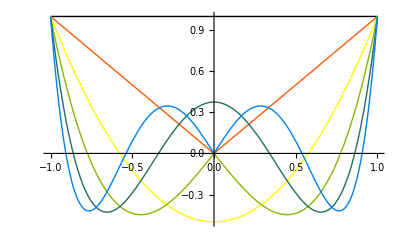

```mathematica
Plot[Evaluate@Table[LegendreP[n,Abs[μ]],{n,0,5}],{μ,-1,1},PlotStyle->ColorData[3,"ColorList"]]
```

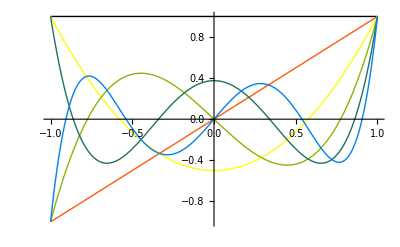

```mathematica
Plot[Evaluate@Table[LegendreP[n,μ],{n,0,5}],{μ,-1,1},PlotStyle->ColorData[3,"ColorList"]]
```

```mathematica
Table[LegendreP[n,μ],{n,0,5}]
```

{1,μ,1/2 (-1+3 μ^2),1/2 (-3 μ+5 μ^3),1/8 (3-30 μ^2+35 μ^4),1/8 (15 μ-70 μ^3+63 μ^5)}